```mathematica
LegendreRecurrsionCoeff[n_,domain_]:=Module[
{βList,αList=ConstantArray[(domain[[2]]+domain[[1]])/2,n],l=(domain[[2]]-domain[[1]])/2},
βList=(l *#)/(√(4#^2-1))&@Range[n-1];
{αList,βList}//N
];
```

```mathematica
VSquared[J_,n_,domain_]:=Module[{αList,βList,M,W,freq,vSq},
{αList,βList}=LegendreRecurrsionCoeff[n,domain];
M=SparseArray[{Band[{1,1}]->αList,Band[{1,2}]->βList,Band[{2,1}]->βList}]//Normal;
{freq,W}=Eigensystem@M;
vSq=J[freq]*(W[[;;,1]]^2*(domain[[2]]-domain[[1]]));
{freq,vSq}={freq[[#]],vSq[[#]]}&@Ordering[freq]
];
```

```mathematica
ApproxSD[J_,n_,domain_,ϵ_]:=Module[
{δ,w,vSq,JApprox},
δ=ϵ/(π(ϵ^2+#^2))&;
{w,vSq}=VSquared[J,n,domain]//N;
Total@(Table[vSq[[i]]*δ[#1-w[[i]]],{i,1,Length[w]}])&];
```

```mathematica
EqFgrRateTwo[Δ_,ε_,kbT_,w_,vSq_]:=Module[{Integrand,k},
Integrand[t_]:=ⅇ^(-1*Total[Table[ vSq[[i]]/(w[[i]]^2 π)(Coth[w[[i]]/(2 kbT)]( 1-Cos[w[[i]]t])+ⅈ Sin[w[[i]]t]),{i,Length[w]}]]);
k=2 Δ^2 Re@NIntegrate[ⅇ^(ⅈ ε t) Integrand[t],{t,0,∞},MaxRecursion->20];
k];
EqFgrRateThreeOrderOne[vList_,εList_,kbT_,w_,sList_]:=Module[{Integrand,prefactor,ε1,ε2,ε3,v12,v13,v23,s1,s2,s3,t1,t2,t3,k1,k2,kc,k},
{v12,v13,v23}=vList;
{s1,s2,s3}=sList;
{ε1,ε2,ε3}=εList;
(*s1=ConstantArray[0,Length[s1]];*)
k1=EqFgrRateTwo[v12,ε1-ε2,kbT,w,s2^2];
k2=EqFgrRateTwo[v13,ε1-ε3,kbT,w,s3^2];
(*Return[$Failed,Module];*)
t1=1000;
Integrand[t1_,t2_,t3_]:=ⅇ^Sum[-Coth[w[[i]]/(2 kbT)](((s1[[i]]-s2[[i]])^2+(s2[[i]]-s3[[i]])^2+(s3[[i]]-s1[[i]])^2)/(2 w[[i]]^2 π))+((s1[[i]]-s2[[i]])(s2[[i]]-s3[[i]]))/(w[[i]]^2 π)(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t1-t2)]+ⅈ Sin[w[[i]](t1-t2)])+((s1[[i]]-s2[[i]])(s3[[i]]-s1[[i]]))/(w[[i]]^2 π)(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t1-t3)]+ⅈ Sin[w[[i]](t1-t3)])+((s2[[i]]-s3[[i]])(s3[[i]]-s1[[i]]))/(w[[i]]^2 π)(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t2-t3)]+ⅈSin[w[[i]](t2-t3)]),{i,Length[w]}];
kc=(-ⅈ)^3 v12×v23×v13×NIntegrate[
ⅇ^(ⅈ (ε1-ε2) t1+ⅈ (ε2-ε3) t2+ⅈ (ε3-ε1)t3) ×
Integrand[t1,t2,t3],{t2,0,t1},{t3,0,t2},Method->{Automatic},PrecisionGoal->3];
(*first-order correction*)
k=k1+k2-4Re@kc];
```

```mathematica
(*(s2[[i]]-s3[[i]])/w[[i]] ⅇ^(ⅈ w[[i]] t2)+*)
```

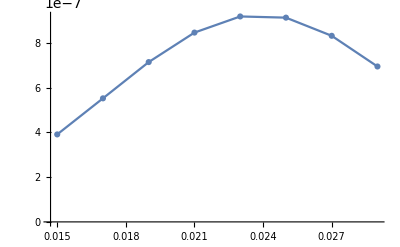

```mathematica
λ=2.39 10^-2;
Ω=3.5 10^-4;
kbT=9.5 10^-4;
η=1.2 10^-3;
domain={0,5 10^-3};
Δ=5 10^-5;
J[ω_]:=(1/2)(4 λ)  ((Ω^2 η ω)/((Ω^2-ω^2)^2+η^2 ω^2));
{w,vSq}=VSquared[J,100,domain];
(*50 is the # of discrete modes*)
Energy=Table[ε,{ε,0.015,.03,0.002}];
RateList=EqFgrRateTwo[Δ,#,kbT,w,vSq]&@Energy;
ListLinePlot[{Energy,RateList}ᵀ,PlotMarkers->Automatic]
```

```mathematica
Energy=Table[ε,{ε,0.015,.03,0.0002}];
RateListA=EqFgrRateThreeOrderOne[{Δ,Δ,10Δ},{0,-#,-#},kbT,w,{-√vSq,√vSq,-√vSq}]&@Energy;
ListLinePlot[{{Energy,RateListA}ᵀ,{Energy, 2RateList}ᵀ},PlotMarkers->Automatic]
RateListB=EqFgrRateThreeOrderOne[{Δ,Δ,10Δ},{0,-#,-#},kbT,w,{-√vSq,√vSq,√vSq}]&@Energy;
ListLinePlot[{{Energy,RateListB}ᵀ,{Energy, 2RateList}ᵀ},PlotMarkers->Automatic]
```

Transpose::nmtx: The first two levels of {{0.015,0.0152,0.0154,0.0156,0.0158,0.016,0.0162,0.0164,0.0166,0.0168,«66»},{7.823×10^-7,1.10491×10^-6,1.4291×10^-6,1.69293×10^-6,1.8371×10^-6,1.8265×10^-6,1.66414×10^-6,1.38976×10^-6}} cannot be transposed.

ListLinePlot::lpn: {{{0.015,7.79984×10^-7},{0.0152,8.1129×10^-7},{0.0154,8.43109×10^-7},{0.0156,8.75374×10^-7},{0.0158,9.08018×10^-7},{0.016,9.40971×10^-7},{0.0162,9.74163×10^-7},{0.0164,1.00752×10^-6},{0.0166,1.04098×10^-6},{0.0168,1.07448×10^-6},«66»},{}} is not a list of numbers or pairs of numbers.

ListLinePlot[{{{0.015,7.79984×10^-7},{0.0152,8.1129×10^-7},{0.0154,8.43109×10^-7},{0.0156,8.75374×10^-7},{0.0158,9.08018×10^-7},{0.016,9.40971×10^-7},{0.0162,9.74163×10^-7},{0.0164,1.00752×10^-6},{0.0166,1.04098×10^-6},{0.0168,1.07448×10^-6},{0.017,1.10794×10^-6},{0.0172,1.1413×10^-6},{0.0174,1.17452×10^-6},{0.0176,1.20753×10^-6},{0.0178,1.24027×10^-6},{0.018,1.27271×10^-6},{0.0182,1.3048×10^-6},{0.0184,1.33648×10^-6},{0.0186,1.36772×10^-6},{0.0188,1.39846×10^-6},{0.019,1.42868×10^-6},{0.0192,1.45832×10^-6},{0.0194,1.48733×10^-6},{0.0196,1.51568×10^-6},{0.0198,1.5433×10^-6},{0.02,1.57015×10^-6},{0.0202,1.59618×10^-6},{0.0204,1.62132×10^-6},{0.0206,1.64551×10^-6},{0.0208,1.66869×10^-6},{0.021,1.6908×10^-6},{0.0212,1.71178×10^-6},{0.0214,1.73154×10^-6},{0.0216,1.75004×10^-6},{0.0218,1.76721×10^-6},{0.022,1.78298×10^-6},{0.0222,1.7973×10^-6},{0.0224,1.81012×10^-6},{0.0226,1.82137×10^-6},{0.0228,1.83104×10^-6},{0.023,1.83906×10^-6},{0.0232,1.84543×10^-6},{0.0234,1.85011×10^-6},{0.0236,1.85309×10^-6},{0.0238,1.85436×10^-6},{0.024,1.85393×10^-6},{0.0242,1.85181×10^-6},{0.0244,1.848×10^-6},{0.0246,1.84255×10^-6},{0.0248,1.83546×10^-6},{0.025,1.82678×10^-6},{0.0252,1.81655×10^-6},{0.0254,1.80481×10^-6},{0.0256,1.7916×10^-6},{0.0258,1.77697×10^-6},{0.026,1.76097×10^-6},{0.0262,1.74366×10^-6},{0.0264,1.72508×10^-6},{0.0266,1.70528×10^-6},{0.0268,1.68432×10^-6},{0.027,1.66225×10^-6},{0.0272,1.63911×10^-6},{0.0274,1.61496×10^-6},{0.0276,1.58983×10^-6},{0.0278,1.56379×10^-6},{0.028,1.53688×10^-6},{0.0282,1.50915×10^-6},{0.0284,1.48064×10^-6},{0.0286,1.45141×10^-6},{0.0288,1.42151×10^-6},{0.029,1.39099×10^-6},{0.0292,1.3599×10^-6},{0.0294,1.32831×10^-6},{0.0296,1.29627×10^-6},{0.0298,1.26384×10^-6},{0.03,1.23109×10^-6}},Transpose[{{0.015,0.0152,0.0154,0.0156,0.0158,0.016,0.0162,0.0164,0.0166,0.0168,0.017,0.0172,0.0174,0.0176,0.0178,0.018,0.0182,0.0184,0.0186,0.0188,0.019,0.0192,0.0194,0.0196,0.0198,0.02,0.0202,0.0204,0.0206,0.0208,0.021,0.0212,0.0214,0.0216,0.0218,0.022,0.0222,0.0224,0.0226,0.0228,0.023,0.0232,0.0234,0.0236,0.0238,0.024,0.0242,0.0244,0.0246,0.0248,0.025,0.0252,0.0254,0.0256,0.0258,0.026,0.0262,0.0264,0.0266,0.0268,0.027,0.0272,0.0274,0.0276,0.0278,0.028,0.0282,0.0284,0.0286,0.0288,0.029,0.0292,0.0294,0.0296,0.0298,0.03},{7.823×10^-7,1.10491×10^-6,1.4291×10^-6,1.69293×10^-6,1.8371×10^-6,1.8265×10^-6,1.66414×10^-6,1.38976×10^-6}}]},PlotMarkers→Automatic]

{-2450.03,-0.000287863}

General::munfl: Exp[-2449.93-822.199 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

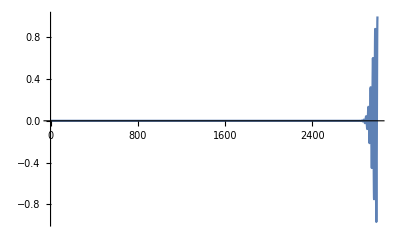
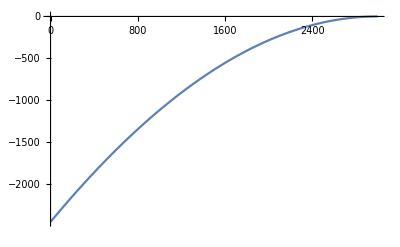

```mathematica
PlotThreeOrderOne[t1_,εList_,kbT_,w_,sList_]:=Module[{Integrand,prefactor,exponent,ε1,ε2,ε3,s1,s2,s3,t2,t3,k1,k2,kc,k},
{s1,s2,s3}=sList;
{ε1,ε2,ε3}=εList;
(*Return[$Failed,Module];*)
t2=t1;
Integrand[t3_]:=Re[ⅇ^Sum[-Coth[w[[i]]/(2 kbT)](((s1[[i]]-s2[[i]])^2+(s2[[i]]-s3[[i]])^2+(s3[[i]]-s1[[i]])^2)/(2 w[[i]]^2))+((s1[[i]]-s2[[i]])(s2[[i]]-s3[[i]]))/w[[i]]^2(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t1-t2)]+ⅈ Sin[w[[i]](t1-t2)])+((s1[[i]]-s2[[i]])(s3[[i]]-s1[[i]]))/w[[i]]^2(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t1-t3)]+ⅈ Sin[w[[i]](t1-t3)])+((s2[[i]]-s3[[i]])(s3[[i]]-s1[[i]]))/w[[i]]^2(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t2-t3)]+ⅈSin[w[[i]](t2-t3)]),{i,Length[w]}]];
exponent[t3_]:=Re[Sum[-Coth[w[[i]]/(2 kbT)](((s1[[i]]-s2[[i]])^2+(s2[[i]]-s3[[i]])^2+(s3[[i]]-s1[[i]])^2)/(2 w[[i]]^2))+((s1[[i]]-s2[[i]])(s2[[i]]-s3[[i]]))/w[[i]]^2(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t1-t2)]+ⅈ Sin[w[[i]](t1-t2)])+((s1[[i]]-s2[[i]])(s3[[i]]-s1[[i]]))/w[[i]]^2(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t1-t3)]+ⅈ Sin[w[[i]](t1-t3)])+((s2[[i]]-s3[[i]])(s3[[i]]-s1[[i]]))/w[[i]]^2(-Coth[w[[i]]/(2 kbT)]Cos[w[[i]](t2-t3)]+ⅈSin[w[[i]](t2-t3)]),{i,Length[w]}]];

Print[Table[exponent[t3],{t3,{0,t2-1}}]];
{Plot[Integrand[t3],{t3,0,t2},PlotRange->All],
Plot[exponent[t3],{t3,0,t2},PlotRange->All]}
];
PlotThreeOrderOne[3000,{0,-0.015,-0.015},kbT,w,{-√vSq,√vSq,√vSq}]
```

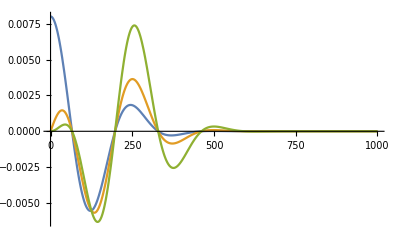

```mathematica
PlotTwo[Δ_,ε_,kbT_,w_,vSq_]:=Module[{Integrand,k},
Integrand[t_]:=Re@(ⅇ^(-1*Total[Table[ vSq[[i]]/(w[[i]]^2 π)(Coth[w[[i]]/(2 kbT)]( 1-Cos[w[[i]]t])+ⅈ Sin[w[[i]]t]),{i,Length[w]}]]));
Plot[{Δ Integrand[t],Δ^2 Integrand[t]t,Δ^3 Integrand[t] t^2},{t,0,1000},PlotRange->All]];
PlotTwo[0.008,0.015,kbT,w,vSq]
```

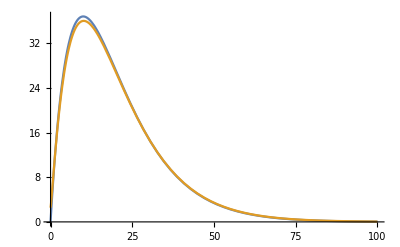

```mathematica
sd=10 # ⅇ^(-#/10)&;
sdApprox=ApproxSD[sd,800,{0,100},0.51/2];
Plot[{sd[x],sdApprox[x]},{x,0,100},PlotRange->Full]
```

```mathematica
NIntegrate[J[x]/x^2,{x,0,1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.63073×10^-29}. NIntegrate obtained 3538.23 and 1392.99 for the integral and error estimates.

3538.23

```mathematica
J[x]/x^2/.x->1
```

7.02676×10^-10